### Giant Manipulate

```mathematica
Manipulate[ param = {e0-> 0.12, e1-> 0.25, thu-> 0.617, thua-> 0.349, thc-> 0.003, thca-> 0.031, gu-> 0.2,gua-> 0.2, gc-> 0.06, gca-> 0.055, ap-> 0.0435, bp-> 0.42,bpa-> 0.42*1.67, bh-> 0.2, bha-> 0.25, n-> 0.4, muc-> 24, vp-> 235, vpa-> 470, vh-> 235, kp-> 0.000004, kpa-> 0.000005, kh-> 0.00001, np-> 23, nh-> 23};
theta[t] = gu*pu[t] + gc*pc[t] +gua*pua[t] + gca*pca[t];
epsilon[t] = e0*(1+e1*Sin[(2Pi)/365*(t-240)]);
sol1 = NDSolve[
{ pu'[t]== thu*theta[t] - ap*bp*(1-n)*pu[t]*hc[t]-kp*pu[t]be[t]-gu*pu[t]-epsilon[t]*pu[t],
pc'[t] == thc*theta[t] +ap*bp*(1-n)*pu[t]*hc[t]+ kp*pu[t]be[t]-gc*pc[t] - epsilon[t]*pc[t],
pua'[t]== thua*theta[t] - ap*bpa*(1-n)*pua[t]*hc[t] - kpa*pua[t]*be[t] - gua*pua[t] +epsilon[t]*pu[t],
pca'[t]== thca*theta[t] + ap*bpa*(1-n)*pua[t]*hc[t] + kpa*pua[t]*be[t] - gca*pca[t] +epsilon[t]*pc[t],
hu'[t] ==  -ap*bh*(1-n)*pc[t]*hu[t] - ap*bha*(1-n)*pca[t]*hu[t] - kh*hu[t]*be[t]+muc*hc[t],
 hc'[t] ==  ap*bh*(1-n)*pc[t]*hu[t] + ap*bha*(1-n)*pca[t]*hu[t] + kh*hu[t]*be[t]-muc*hc[t],
be'[t] == vp*pc[t]+ vpa*pca[t]+vh*hc[t]-gb*be[t],
pu[0]== 4, pua[0]==6,pc[0]== 7, pca[0]==6, hu[0]==17, hc[0]==6, be[0]==1000}/. param,
 {pu[t], pua[t],pc[t], pca[t], hu[t], hc[t], be[t]},{t, 0,1000}
];
Plot[Evaluate[{pu[t], pua[t],pc[t], pca[t] }/.sol1],{t,0,1000},PlotRange->{{0,1000},{0,10}}, PlotStyle->{Blue,Red,Purple, Yellow},AxesLabel-> {"Time (days)", "Number"}], {{gb, 0.7},0.6,1}
]
```

### Figure 4 and 5

```mathematica
param = {e0-> 0.12, e1-> 0.25, thu-> 0.617, thua-> 0.349, thc-> 0.003, thca-> 0.031, gu-> 0.2,gua-> 0.2, gc-> 0.06, gca-> 0.055, gb-> 0.7, ap-> 0.0435, bp-> 0.42,bpa-> 0.42*1.67, bh-> 0.2, bha-> 0.25, n-> 0.4, muc-> 24, vp-> 235, vpa-> 470, vh-> 235, kp-> 0.000004, kpa-> 0.000005, kh-> 0.00001, np-> 23, nh-> 23};
```

```mathematica
theta[t] = gu*pu[t] + gc*pc[t] +gua*pua[t] + gca*pca[t];
epsilon[t] = e0*(1+e1*Sin[(2Pi)/365*(t-240)]);
```

```mathematica
sol1 = NDSolve[
{ pu'[t]== thu*theta[t] - ap*bp*(1-n)*pu[t]*hc[t]-kp*pu[t]be[t]-gu*pu[t]-epsilon[t]*pu[t],
pc'[t] == thc*theta[t] +ap*bp*(1-n)*pu[t]*hc[t]+ kp*pu[t]be[t]-gc*pc[t] - epsilon[t]*pc[t],
pua'[t]== thua*theta[t] - ap*bpa*(1-n)*pua[t]*hc[t] - kpa*pua[t]*be[t] - gua*pua[t] +epsilon[t]*pu[t],
pca'[t]== thca*theta[t] + ap*bpa*(1-n)*pua[t]*hc[t] + kpa*pua[t]*be[t] - gca*pca[t] +epsilon[t]*pc[t],
hu'[t] ==  -ap*bh*(1-n)*pc[t]*hu[t] - ap*bha*(1-n)*pca[t]*hu[t] - kh*hu[t]*be[t]+muc*hc[t],
 hc'[t] ==  ap*bh*(1-n)*pc[t]*hu[t] + ap*bha*(1-n)*pca[t]*hu[t] + kh*hu[t]*be[t]-muc*hc[t],
be'[t] == vp*pc[t]+ vpa*pca[t]+vh*hc[t]-gb*be[t],
pu[0]== 4, pua[0]==6,pc[0]== 7, pca[0]==6, hu[0]==17, hc[0]==6, be[0]==1000}/. param,
 {pu[t], pua[t],pc[t], pca[t], hu[t], hc[t], be[t]},{t, 0,1000}
];
```

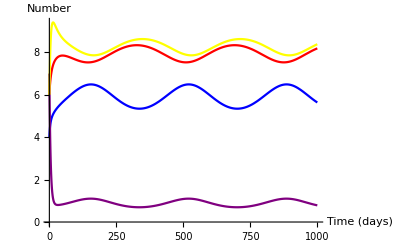

```mathematica
Plot[Evaluate[{pu[t], pua[t],pc[t], pca[t] }/.sol1],{t,0,1000},PlotRange->Automatic, PlotStyle->{Blue,Red,Purple, Yellow},AxesLabel-> {"Time (days)", "Number"}]
```

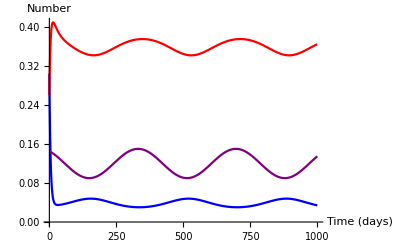

```mathematica
Plot[Evaluate[{pc[t]/(pu[t]+pua[t]+pc[t]+pca[t]  ), pca[t]/(pu[t]+pua[t]+pc[t]+pca[t]  ), epsilon[t]/.param  }/.sol1],{t,0,1000},PlotRange->Automatic, PlotStyle->{Blue,Red,Purple},AxesLabel-> {"Time (days)", "Number"}]
```

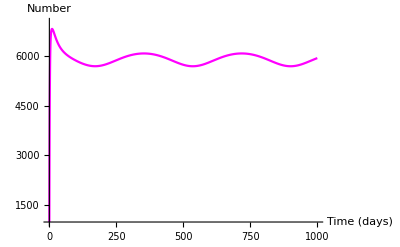

```mathematica
Plot[Evaluate[{be[t] }/.sol1],{t,0,1000},PlotRange->{{0,1000},{1000,7000}}, PlotStyle->{Magenta},AxesLabel-> {"Time (days)", "Number"}]
```

### Figure 6

```mathematica
param2= {e0-> 0.12, e1-> 0.25, thu-> 0.62, thua-> 0.38, thc-> 0., thca-> 0., gu-> 0.2,gua-> 0.2, gc-> 0.06, gca-> 0.055, gb-> 0.7, ap-> 0.0435, bp-> 0.42,bpa-> 0.42*1.67, bh-> 0.2, bha-> 0.25, n-> 0.4, muc-> 24, vp-> 235, vpa-> 470, vh-> 235, kp-> 0.000004, kpa-> 0.000005, kh-> 0.00001, np-> 23, nh-> 23};
```

```mathematica
theta[t] = gu*pu[t] + gc*pc[t] +gua*pua[t] + gca*pca[t];
epsilon[t] = e0*(1+e1*Sin[(2Pi)/365*(t-240)]);
```

```mathematica
sol2 = NDSolve[
{ pu'[t]== thu*theta[t] - ap*bp*(1-n)*pu[t]*hc[t]-kp*pu[t]be[t]-gu*pu[t]-epsilon[t]*pu[t],
pc'[t] == thc*theta[t] +ap*bp*(1-n)*pu[t]*hc[t]+ kp*pu[t]be[t]-gc*pc[t] - epsilon[t]*pc[t],
pua'[t]== thua*theta[t] - ap*bpa*(1-n)*pua[t]*hc[t] - kpa*pua[t]*be[t] - gua*pua[t] +epsilon[t]*pu[t],
pca'[t]== thca*theta[t] + ap*bpa*(1-n)*pua[t]*hc[t] + kpa*pua[t]*be[t] - gca*pca[t] +epsilon[t]*pc[t],
hu'[t] ==  -ap*bh*(1-n)*pc[t]*hu[t] - ap*bha*(1-n)*pca[t]*hu[t] - kh*hu[t]*be[t]+muc*hc[t],
 hc'[t] ==  ap*bh*(1-n)*pc[t]*hu[t] + ap*bha*(1-n)*pca[t]*hu[t] + kh*hu[t]*be[t]-muc*hc[t],
be'[t] == vp*pc[t]+ vpa*pca[t]+vh*hc[t]-gb*be[t],
pu[0]== 4, pua[0]==6,pc[0]== 7, pca[0]==6, hu[0]==17, hc[0]==6, be[0]==1000}/. param2,
 {pu[t], pua[t],pc[t], pca[t], hu[t], hc[t], be[t]},{t, 0,1000}
];
```

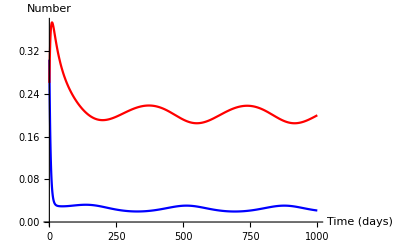

```mathematica
Plot[Evaluate[{pc[t]/(pu[t]+pua[t]+pc[t]+pca[t]  ), pca[t]/(pu[t]+pua[t]+pc[t]+pca[t]  )}/.sol2],{t,0,1000},PlotRange->Automatic, PlotStyle->{Blue,Red},AxesLabel-> {"Time (days)", "Number"}]
```

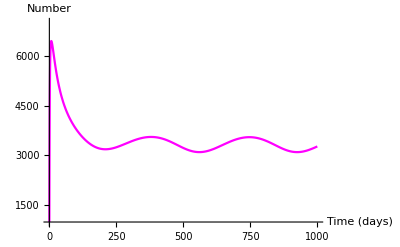

```mathematica
Plot[Evaluate[{be[t] }/.sol2],{t,0,1000},PlotRange->{{0,1000},{1000,7000}}, PlotStyle->{Magenta},AxesLabel-> {"Time (days)", "Number"}]
```

### Figure 7

```mathematica
param3= {e0-> 0.12, e1-> 0.25, thu-> 1., thua-> 0., thc-> 0., thca-> 0., gu-> 0.2,gua-> 0.2, gc-> 0.06, gca-> 0.055, gb-> 0.7, ap-> 0.0435, bp-> 0.42,bpa-> 0.42*1.67, bh-> 0.2, bha-> 0.25, n-> 0.4, muc-> 24, vp-> 235, vpa-> 470, vh-> 235, kp-> 0.000004, kpa-> 0.000005, kh-> 0.00001, np-> 23, nh-> 23};
```

```mathematica
theta[t] = gu*pu[t] + gc*pc[t] +gua*pua[t] + gca*pca[t];
epsilon[t] = e0*(1+e1*Sin[(2Pi)/365*(t-240)]);
```

```mathematica
sol3= NDSolve[
{ pu'[t]== thu*theta[t] - ap*bp*(1-n)*pu[t]*hc[t]-kp*pu[t]be[t]-gu*pu[t]-epsilon[t]*pu[t],
pc'[t] == thc*theta[t] +ap*bp*(1-n)*pu[t]*hc[t]+ kp*pu[t]be[t]-gc*pc[t] - epsilon[t]*pc[t],
pua'[t]== thua*theta[t] - ap*bpa*(1-n)*pua[t]*hc[t] - kpa*pua[t]*be[t] - gua*pua[t] +epsilon[t]*pu[t],
pca'[t]== thca*theta[t] + ap*bpa*(1-n)*pua[t]*hc[t] + kpa*pua[t]*be[t] - gca*pca[t] +epsilon[t]*pc[t],
hu'[t] ==  -ap*bh*(1-n)*pc[t]*hu[t] - ap*bha*(1-n)*pca[t]*hu[t] - kh*hu[t]*be[t]+muc*hc[t],
 hc'[t] ==  ap*bh*(1-n)*pc[t]*hu[t] + ap*bha*(1-n)*pca[t]*hu[t] + kh*hu[t]*be[t]-muc*hc[t],
be'[t] == vp*pc[t]+ vpa*pca[t]+vh*hc[t]-gb*be[t],
pu[0]== 4, pua[0]==6,pc[0]== 7, pca[0]==6, hu[0]==17, hc[0]==6, be[0]==1000}/. param3,
 {pu[t], pua[t],pc[t], pca[t], hu[t], hc[t], be[t]},{t, 0,1000}
];
```

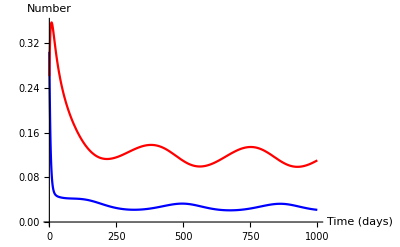

```mathematica
Plot[Evaluate[{pc[t]/(pu[t]+pua[t]+pc[t]+pca[t]  ), pca[t]/(pu[t]+pua[t]+pc[t]+pca[t]  )}/.sol3],{t,0,1000},PlotRange->Automatic, PlotStyle->{Blue,Red},AxesLabel-> {"Time (days)", "Number"}]
```

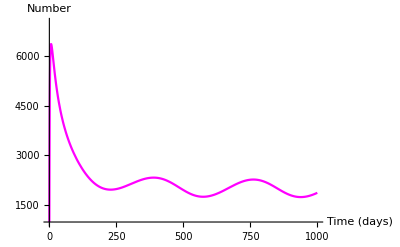

```mathematica
Plot[Evaluate[{be[t] }/.sol3],{t,0,1000},PlotRange->{{0,1000},{1000,7000}}, PlotStyle->{Magenta},AxesLabel-> {"Time (days)", "Number"}]
```

## BRN Stuff - Ooh Child!

```mathematica
fvMatrix = {{-(gc+epsilon[t]),0,0,0},{epsilon[t],-gca,(ap bpa (1-n)np)/lambda, (kpa np)/lambda},{(ap bh (1-n)nh)/lambda,(ap bha (1-n)nh)/lambda ,-muc ,(kh nh)/lambda },{vp, vpa, vh, -gb}};
```

```mathematica
fvMatrix //MatrixForm
```

(-gc-e0 (1+e1 Sin[2/365 π (-240+t)]) | 0 | 0 | 0
e0 (1+e1 Sin[2/365 π (-240+t)]) | -gca | (ap bpa (1-n) np)/lambda | (kpa np)/lambda
(ap bh (1-n) nh)/lambda | (ap bha (1-n) nh)/lambda | -muc | (kh nh)/lambda
vp | vpa | vh | -gb)

```mathematica
(*No gamma_b*)
```

```mathematica
param2= {e0-> 0.12, e1-> 0.25, thu-> 0.617, thua-> 0.349, thc-> 0.003, thca-> 0.031, gu-> 0.2,gua-> 0.2, gc-> 0.06, gca-> 0.055, ap-> 0.0435, bp-> 0.42,bpa-> 0.42*1.67, bh-> 0.2, bha-> 0.25, n-> 0.4, muc-> 24, vp-> 235, vpa-> 470, vh-> 235, kp-> 0.000004, kpa-> 0.000005, kh-> 0.00001, np-> 23, nh-> 23};
```

```mathematica
fvMatrix/.param2//MatrixForm
```

(-0.06-0.12 (1+0.25 Sin[2/365 π (-240+t)]) | 0 | 0 | 0
0.12 (1+0.25 Sin[2/365 π (-240+t)]) | -0.055 | 0.42105/lambda | 0.000115/lambda
0.12006/lambda | 0.150075/lambda | -24 | 0.00023/lambda
235 | 470 | 235 | -gb)

```mathematica
extraparam = {gb-> 0.7, lambda-> 1.476, t-> 2Pi};
```

```mathematica
testMat = fvMatrix/.param2/.extraparam
```

{{-0.203154,0,0,0},{0.143154,-0.055,0.285265,0.0000779133},{0.0813415,0.101677,-24,0.000155827},{235,470,235,-0.7}}

```mathematica
(Max[Eigenvalues[MatrixExp[testMat t]/.{t->2Pi}]] - 1 )*100
```

-0.00232431

```mathematica
MatrixExp[testMat t]/.extraparam//MatrixForm
```

(0.279025 | 3.35935×10^-14 | 4.41055×10^-16 | 4.27069×10^-18
0.556318 | 0.929014 | 0.0120711 | 0.000105081
0.00617602 | 0.00796338 | 0.000104099 | 9.64356×10^-7
443.338 | 620.484 | 8.15611 | 0.0797158)

```mathematica
Eigenvalues[%]
```

{0.999977,0.279025,0.00885695,-4.26792×10^-20}

```mathematica
Max[%]
```

0.999977

```mathematica
Abs[(1-%)*100]
```

0.00232431

```mathematica
Abs[(Max[Eigenvalues[MatrixExp[testMat t]/.{t->2Pi}]] - 1 )*100]
```

0.0932308

```mathematica
%<0.01
```

False

### BRN - Figure 8 (a)

```mathematica
Remove[funcgb]
```

```mathematica
funcgb[gbval_]:= Module[{param,fvMatrix, extraparam,val1,testMat,start},
param= {e0-> 0.12, e1-> 0.25, thu-> 0.617, thua-> 0.349, thc-> 0.003, thca-> 0.031, gu-> 0.2,gua-> 0.2, gc-> 0.06, gca-> 0.055, ap-> 0.0435, bp-> 0.42,bpa-> 0.42*1.67, bh-> 0.2, bha-> 0.25, n-> 0.4, muc-> 24, vp-> 235, vpa-> 470, vh-> 235, kp-> 0.000004, kpa-> 0.000005, kh-> 0.00001, np-> 23, nh-> 23};
theta[t] = gu*pu[t] + gc*pc[t] +gua*pua[t] + gca*pca[t];
epsilon[t] = e0*(1+e1*Sin[(2Pi)/365*(t-240)]);
fvMatrix = {{-(gc+epsilon[t]),0,0,0},{epsilon[t],-gca,(ap bpa (1-n)np)/lambda, (kpa np)/lambda},{(ap bh (1-n)nh)/lambda,(ap bha (1-n)nh)/lambda ,-muc ,(kh nh)/lambda },{vp, vpa, vh, -gb}};
start =1.710;
extraparam =  {gb-> gbval, lambda-> start, t-> 2Pi};
testMat = fvMatrix/.param/.extraparam;

While[Abs[(Max[Eigenvalues[MatrixExp[testMat t]/.{t->2Pi}]] - 1 )*100]>0.04,
start = start -0.001;
extraparam =  {gb-> gbval, lambda-> start, t-> 2Pi};
testMat = fvMatrix/.param/.extraparam;
maybe = start;
];
Return[start-0.001]
]
```

```mathematica
funcgb[0.7]
```

1.476

```mathematica
testData1 = Table[{x,(funcgb[x])},{x,0.6,1,0.05}];
```

```mathematica
testData1
```

{{0.6,1.707},{0.65,1.583},{0.7,1.476},{0.75,1.384},{0.8,1.304},{0.85,1.233},{0.9,1.171},{0.95,1.115},{1.,1.065}}

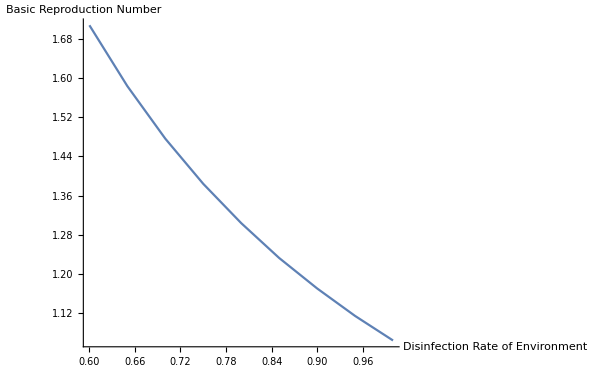

```mathematica
ListLinePlot[testData1, AxesLabel->{"Disinfection Rate of Environment","Basic Reproduction Number"}]
```

### BRN - Figure 8 (b)

```mathematica
Remove[funcvpa]
```

```mathematica
funcvpa[vpaval_]:= Module[{param,fvMatrix, extraparam,val1,testMat,start},
param= {e0-> 0.12, e1-> 0.25, thu-> 0.617, thua-> 0.349, thc-> 0.003, thca-> 0.031, gu-> 0.2,gua-> 0.2, gc-> 0.06, gca-> 0.055, gb-> 0.7,ap-> 0.0435, bp-> 0.42,bpa-> 0.42*1.67, bh-> 0.2, bha-> 0.25, n-> 0.4, muc-> 24, vp-> 235, vh-> 235, kp-> 0.000004, kpa-> 0.000005, kh-> 0.00001, np-> 23, nh-> 23};
theta[t] = gu*pu[t] + gc*pc[t] +gua*pua[t] + gca*pca[t];
epsilon[t] = e0*(1+e1*Sin[(2Pi)/365*(t-240)]);
fvMatrix = {{-(gc+epsilon[t]),0,0,0},{epsilon[t],-gca,(ap bpa (1-n)np)/lambda, (kpa np)/lambda},{(ap bh (1-n)nh)/lambda,(ap bha (1-n)nh)/lambda ,-muc ,(kh nh)/lambda },{vp, vpa, vh, -gb}};
start =0.800;
extraparam =  {vpa-> vpaval, lambda-> start, t-> 2Pi};
testMat = fvMatrix/.param/.extraparam;

While[Abs[(Max[Eigenvalues[MatrixExp[testMat t]/.{t->2Pi}]] - 1 )*100]>0.04,
start = start +0.001;
extraparam =  {vpa-> vpaval, lambda-> start, t-> 2Pi};
testMat = fvMatrix/.param/.extraparam;
maybe = start;
];
Return[start-0.001]
]
```

```mathematica
funcvpa[300]
```

0.983

```mathematica
testData2 = Table[{x,(funcvpa[x])},{x,250,480,1}];
```

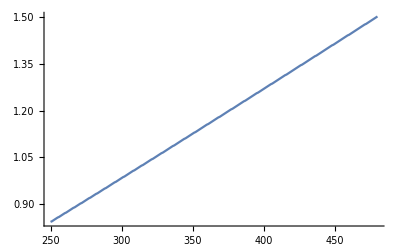

```mathematica
ListLinePlot[testData2]
```

### BRN - Figure 8 (c)

```mathematica
Remove[funcgca]
```

```mathematica
funcgca[gcaval_]:= Module[{param,fvMatrix, extraparam,val1,testMat,start},
param= {e0-> 0.12, e1-> 0.25, thu-> 0.617, thua-> 0.349, thc-> 0.003, thca-> 0.031, gb-> 0.7, gu-> 0.2,gua-> 0.2, gc-> 0.06,  ap-> 0.0435, bp-> 0.42,bpa-> 0.42*1.67, bh-> 0.2, bha-> 0.25, n-> 0.4, muc-> 24, vp-> 235, vpa-> 470, vh-> 235, kp-> 0.000004, kpa-> 0.000005, kh-> 0.00001, np-> 23, nh-> 23};
theta[t] = gu*pu[t] + gc*pc[t] +gua*pua[t] + gca*pca[t];
epsilon[t] = e0*(1+e1*Sin[(2Pi)/365*(t-240)]);
fvMatrix = {{-(gc+epsilon[t]),0,0,0},{epsilon[t],-gca,(ap bpa (1-n)np)/lambda, (kpa np)/lambda},{(ap bh (1-n)nh)/lambda,(ap bha (1-n)nh)/lambda ,-muc ,(kh nh)/lambda },{vp, vpa, vh, -gb}};
start =4.500;
extraparam =  {gca-> gcaval, lambda-> start, t-> 2Pi};
testMat = fvMatrix/.param/.extraparam;

While[Abs[(Max[Eigenvalues[MatrixExp[testMat t]/.{t->2Pi}]] - 1 )*100]>0.04,
start = start -0.001;
extraparam =  {gca-> gcaval, lambda-> start, t-> 2Pi};
testMat = fvMatrix/.param/.extraparam;
maybe = start;
];
Return[start-0.001]
]
```

```mathematica
funcgca[0.018]
```

4.378

```mathematica
Remove[testData3]
```

```mathematica
testData3 = Table[{x,(funcgca[x])},{x,0.018,0.2,0.03}];
```

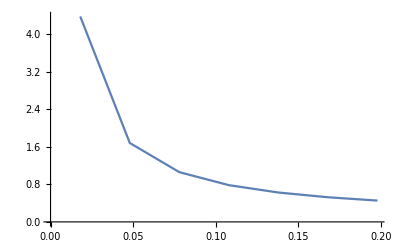

```mathematica
ListLinePlot[testData3]
```

### BRN - Figure 8 (d)

```mathematica
Remove[funcn]
```

```mathematica
funcn[nval_]:= Module[{param,fvMatrix, extraparam,val1,testMat,start},
param= {e0-> 0.12, e1-> 0.25, thu-> 0.617, thua-> 0.349, thc-> 0.003, thca-> 0.031, gu-> 0.2,gua-> 0.2, gc-> 0.06, gca-> 0.055, gb-> 0.7,ap-> 0.0435, bp-> 0.42,bpa-> 0.42*1.67, bh-> 0.2, bha-> 0.25, muc-> 24, vp-> 235, vpa-> 470, vh-> 235, kp-> 0.000004, kpa-> 0.000005, kh-> 0.00001, np-> 23, nh-> 23};
theta[t] = gu*pu[t] + gc*pc[t] +gua*pua[t] + gca*pca[t];
epsilon[t] = e0*(1+e1*Sin[(2Pi)/365*(t-240)]);
fvMatrix = {{-(gc+epsilon[t]),0,0,0},{epsilon[t],-gca,(ap bpa (1-n)np)/lambda, (kpa np)/lambda},{(ap bh (1-n)nh)/lambda,(ap bha (1-n)nh)/lambda ,-muc ,(kh nh)/lambda },{vp, vpa, vh, -gb}};
start =1.480;
extraparam =  {n-> nval, lambda-> start, t-> 2Pi};
testMat = fvMatrix/.param/.extraparam;

While[Abs[(Max[Eigenvalues[MatrixExp[testMat t]/.{t->2Pi}]] - 1 )*100]>0.04,
start = start -0.001;
extraparam =  {n-> nval, lambda-> start, t-> 2Pi};
testMat = fvMatrix/.param/.extraparam;
maybe = start;
];
Return[start-0.001]
]
```

```mathematica
funcn[0.4]
```

1.476

```mathematica
testData4 = Table[{x,(funcn[x])},{x,0.4,1,0.05}];
```

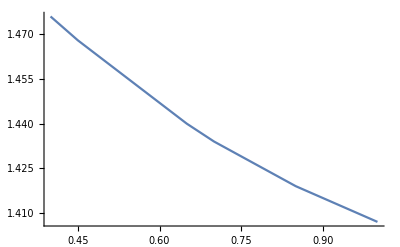

```mathematica
ListLinePlot[testData4]
```

### BRN - Figure 8 (e)

```mathematica
Remove[funcap]
```

```mathematica
funcap[apval_]:= Module[{param,fvMatrix, extraparam,val1,testMat,start},
param= {e0-> 0.12, e1-> 0.25, thu-> 0.617, thua-> 0.349, thc-> 0.003, thca-> 0.031, gu-> 0.2,gua-> 0.2, gc-> 0.06, gca-> 0.055, gb-> 0.7, bp-> 0.42,bpa-> 0.42*1.67, bh-> 0.2, bha-> 0.25, n-> 0.4, muc-> 24, vp-> 235, vpa-> 470, vh-> 235, kp-> 0.000004, kpa-> 0.000005, kh-> 0.00001, np-> 23, nh-> 23};
theta[t] = gu*pu[t] + gc*pc[t] +gua*pua[t] + gca*pca[t];
epsilon[t] = e0*(1+e1*Sin[(2Pi)/365*(t-240)]);
fvMatrix = {{-(gc+epsilon[t]),0,0,0},{epsilon[t],-gca,(ap bpa (1-n)np)/lambda, (kpa np)/lambda},{(ap bh (1-n)nh)/lambda,(ap bha (1-n)nh)/lambda ,-muc ,(kh nh)/lambda },{vp, vpa, vh, -gb}};
start =1.405;
extraparam =  {ap-> apval, lambda-> start, t-> 2Pi};
testMat = fvMatrix/.param/.extraparam;

While[Abs[(Max[Eigenvalues[MatrixExp[testMat t]/.{t->2Pi}]] - 1 )*100]>0.04,
start = start +0.001;
extraparam =  {ap-> apval, lambda-> start, t-> 2Pi};
testMat = fvMatrix/.param/.extraparam;
maybe = start;
];
Return[start-0.001]
]
```

```mathematica
funcap[0]
```

1.405

```mathematica
testData5 = Table[{x,(funcap[x])},{x,0.,0.05,0.01}];
```

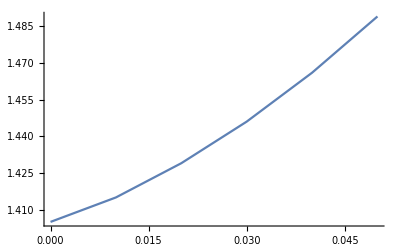

```mathematica
ListLinePlot[testData5]
```

### BRN - Figure 8 (f)

```mathematica
Remove[funcmuc]
```

```mathematica
funcmuc[mucval_]:= Module[{param,fvMatrix, extraparam,val1,testMat,start},
param= {e0-> 0.12, e1-> 0.25, thu-> 0.617, thua-> 0.349, thc-> 0.003, thca-> 0.031, gu-> 0.2,gua-> 0.2, gc-> 0.06, gca-> 0.055,gb-> 0.7, ap-> 0.0435, bp-> 0.42,bpa-> 0.42*1.67, bh-> 0.2, bha-> 0.25, n-> 0.4,  vp-> 235, vpa-> 470, vh-> 235, kp-> 0.000004, kpa-> 0.000005, kh-> 0.00001, np-> 23, nh-> 23};
theta[t] = gu*pu[t] + gc*pc[t] +gua*pua[t] + gca*pca[t];
epsilon[t] = e0*(1+e1*Sin[(2Pi)/365*(t-240)]);
fvMatrix = {{-(gc+epsilon[t]),0,0,0},{epsilon[t],-gca,(ap bpa (1-n)np)/lambda, (kpa np)/lambda},{(ap bh (1-n)nh)/lambda,(ap bha (1-n)nh)/lambda ,-muc ,(kh nh)/lambda },{vp, vpa, vh, -gb}};
start =1.485;
extraparam =  {muc-> mucval, lambda-> start, t-> 2Pi};
testMat = fvMatrix/.param/.extraparam;

While[Abs[(Max[Eigenvalues[MatrixExp[testMat t]/.{t->2Pi}]] - 1 )*100]>0.04,
start = start -0.001;
extraparam =  {muc-> mucval, lambda-> start, t-> 2Pi};
testMat = fvMatrix/.param/.extraparam;
maybe = start;
];
Return[start-0.001]
]
```

```mathematica
funcmuc[24]
```

1.476

```mathematica
testData6 = Table[{x,(funcmuc[x])},{x,21,60,1}];
```

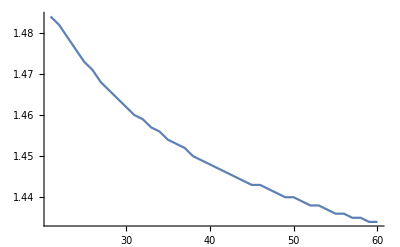

```mathematica
ListLinePlot[testData6]
```